### Speed of a Quantum Walk

```mathematica
L=11;
```

```mathematica
M=Table[If[Abs[i-j]<= 1, If[i==j,0, 1], 0],{i, 1, L}, {j, 1, L}];
Val = Eigenvalues[M]//N;
Vec = Eigenvectors[Transpose[M]]//N;
Sol = Solve[Table[If[i==Ceiling[L/2], 1, 0], {i, 1, L}]==Sum[c[k] Vec[[k]], {k, 1, L}], Table[c[k], {k, 1, L}] ];
Coeff = Table[Sol[[1]][[i]][[2]], {i, 1, L}];
```

```mathematica
Psi[t_]:=Sum[Coeff[[k]] Vec[[k]] Exp[- I Val[[k]] t], {k, 1, L}]
Qprob[t_]:=Table[Abs[Psi[t][[k]]]^2, {k, 1, L}]
QprobAvg[t_]:= If[t==0, Qprob[0],(1/t)NIntegrate[Qprob[s], {s, 0, t}]]
```

```mathematica
Sum[QprobAvg[1][[k]], {k, 1, L}]
```

1.

```mathematica
plot =Flatten[Table[{k, t, QprobAvg[t][[k]]}, {k ,1, L}, {t, 0, 10, 1}],1];
```

```mathematica
ListPlot3D[plot, PlotRange->All]
```

-Graphics3D-

```mathematica
QEval[t_]:= Sum[k QprobAvg[t][[k]], {k, 1, L}];
```

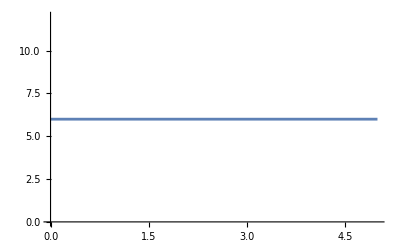

```mathematica
ListPlot[Table[{t, QEval[t]}, {t, 0, 5, 1}], Joined -> True]
```

```mathematica
Ceiling[L/2]
```

6

```mathematica
QSD[t_]:= (Sum[k^2 QprobAvg[t][[k]], {k, 1, L}] - Ceiling[L/2]^2)^(1/2);
```

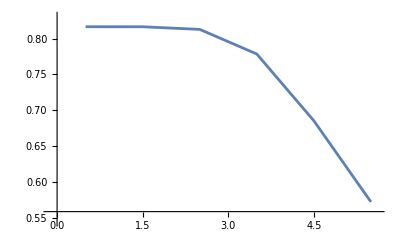

```mathematica
ListPlot[Table[{t, QSD[t]/t}, {t, 0.5, 5.5, 1}], Joined -> True]
```

```mathematica
N[√(2/3)]
```

0.816497

```mathematica
QSD[1/2]/(1/2)
```

0.816497

### Speed of a Quantum Walk

```mathematica
L=11;
J=2;
```

```mathematica
M=Table[If[Abs[i-j]<= 1, If[i==j,0, J], 0],{i, 1, L}, {j, 1, L}];
Val = Eigenvalues[M]//N;
Vec = Eigenvectors[Transpose[M]]//N;
Sol = Solve[Table[If[i==Ceiling[L/2], 1, 0], {i, 1, L}]==Sum[c[k] Vec[[k]], {k, 1, L}], Table[c[k], {k, 1, L}] ];
Coeff = Table[Sol[[1]][[i]][[2]], {i, 1, L}];
```

```mathematica
Psi[t_]:=Sum[Coeff[[k]] Vec[[k]] Exp[- I Val[[k]] t], {k, 1, L}]
Qprob[t_]:=Table[Abs[Psi[t][[k]]]^2, {k, 1, L}]
QprobAvg[t_]:= If[t==0, Qprob[0],(1/t)NIntegrate[Qprob[s], {s, 0, t}]]
```

```mathematica
Sum[QprobAvg[1][[k]], {k, 1, L}]
```

1.

```mathematica
plot =Flatten[Table[{k, t, QprobAvg[t][[k]]}, {k ,1, L}, {t, 0, 10, 1}],1];
```

```mathematica
ListPlot3D[plot, PlotRange->All]
```

-Graphics3D-

```mathematica
QEval[t_]:= Sum[k QprobAvg[t][[k]], {k, 1, L}];
```

```mathematica
ListPlot[Table[{t, QEval[t]}, {t, 0, 5, 1}], Joined -> True]
```

-Graphics-

```mathematica
Ceiling[L/2]
```

6

```mathematica
QSD[t_]:= (Sum[k^2 QprobAvg[t][[k]], {k, 1, L}] - Ceiling[L/2]^2)^(1/2);
```

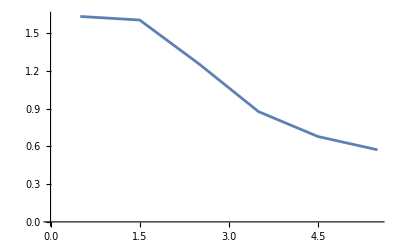

```mathematica
ListPlot[Table[{t, QSD[t]/t}, {t, 0.5, 5.5, 1}], Joined -> True]
```

```mathematica
N[J √(2 /3)]
```

1.63299

```mathematica
QSD[1/2]/(1/2)
```

1.63299

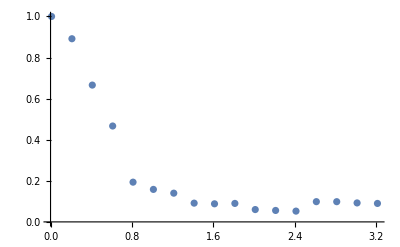

```mathematica
ListPlot[Table[{t, QprobAvg[t][[Floor[L/2]+Min[Ceiling[J t √(2/3)],Ceiling[L/2]]]]}, {t, 0.01, L/(2 J √(2/3)), 0.2}]]
```

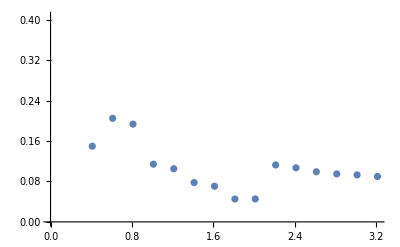

```mathematica
ListPlot[Table[{t, QprobAvg[t][[Floor[L/2]+Min[Ceiling[(1.5)J t √(2/3)],Ceiling[L/2]]]]}, {t, 0.01, L/(2 J √(2/3)), 0.2}]]
```

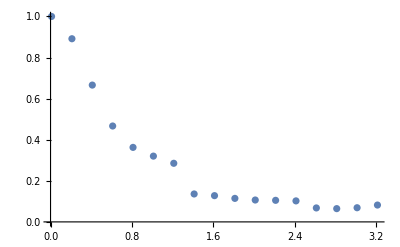

```mathematica
ListPlot[Table[{t, QprobAvg[t][[Floor[L/2]+Min[Ceiling[(0.5)J t √(2/3)],Ceiling[L/2]]]]}, {t, 0.01, L/(2 J √(2/3)), 0.2}]]
```

```mathematica
Floor[L/2]+Min[Ceiling[J t √(2/3)],Ceiling[L/2]]/. t->0.01
```

6

```mathematica
Ceiling[.1]
```

1

### Prob Function along the wave front